## Машинное обучение

##### Постановка задачи.

Задано множество объектов Х, множество допустимых ответов Y, и существует целевая функция y^*:X→Y, значения которой y_i=y^*(x_i) известны только на конечном подмножестве объектов {x_1,...,x_l}⊂X. Пары “объект-ответ” (x_i,y_i) называются прецедентами. Совокупность пар X^l=(x_i,y_i)_(i=1)^l называется обучающей выборкой.

Задача обучения по прецедентам заключается в том, чтобы по обучающей выборке восстановить зависимость y^*, то есть построить решающую функцию (алгоритм) a:X→Y, которая приближала бы целевую функцию y^*(x), причём не только на объектах обучающей выборки, но и на всём множестве X.

В зависимости от природы множестве допустимых ответов задачи обучения по прецедентам делятся на несколько типом. В случае если Y={1,...,M} то это задача классификации на M непересекающихся классов. В этом случае всё множество объектов X разбивается на классы K_y={x∈X:y^*(x)=y}, и алгоритм a(x) должен давать ответ на вопрос “какому классу принадлежит x?”.

Рассмотрим базовой метод классификации:

##### Метрический метод классификации

Пусть на множестве объектов Х задана функция расстояния r:X×X→ [0,∞). Для произвольного объекта u∈X расположим элементы обучающей выборки в порядке возрастания расстояний до u:

r(u,x_u^(1))≤ r(u,x_u^(2))≤ ...r(u,x_u^(l))

Воспользуемся гипотезой компактности, которая утверждает следующее:

Схожие объекты, как правило, лежат в одном классе.

Тогда, метрический алгоритм классификации с обучающей выборкой X^l относит объект u к тому классу y∈Y, для которого суммарный вес ближайших обучающих объектов Г_y(u,X^l) максимален.

a(u,X^l)=arg max_(y∈Y) Г_y(u,X^l)

Г_y(u,X^l)=∑_(i=1)^l [y_u^(i)=y]ω(i,u)
где ω(i,u)- весовая функция, оценивает степень значимости i-ого соседа для классификации объекта u,
Г_y(u,X^l)- оценка близости объекта u к классу y.

В зависимости от вида функции ω(i,u), метод называется:

Метод ближайшего соседа: ω(i,u)=[i=1]→ a(u,X^l)=y_u^(1), т.е учитывается только ближайший сосед.
Метод k-ближайших соседей:ω(i,u)=[i≤k], т.е учитывается k ближайших соседей.

Существуют также и другие весовые функции, но на них подробно останавливаться не будем.

Рассмотрим наиболее известную обучающую задачу классификации:

## Ирисы Фишера

Задача состоит из данных о 150 экземплярах ириса, по 50 экземпляров из трёх видов -  Ирис щетинистый (Iris setosa), Ирис виргинский (Iris virginica) и Ирис разноцветный (Iris versicolor). Для каждого экземпляра измерялись четыре характеристики (в сантиметрах):

1. Длина наружной доли околоцветника (англ. sepal length);
2. Ширина наружной доли околоцветника (англ. sepal width);
3. Длина внутренней доли околоцветника (англ. petal length);
4. Ширина внутренней доли околоцветника (англ. petal width).

На основании этого набора данных требуется построить правило классификации, определяющее вид растения по данным измерений.

Импортируем обучающую выборку с сайта http://archive.ics.uci.edu/ml/ (Machine Learning Repository.)

```mathematica
ld=Drop[Import[ "http://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data"],-1];
```

Каждый элемент имеет вид:

```mathematica
ld[[1]]
```

{5.1,3.5,1.4,0.2,Iris-setosa}

Где первый элемент соответственно Длина наружной доли околоцветника и т.д.

Составим диаграмму рассеяния для каждой пары данных:

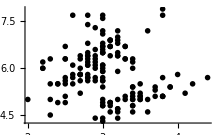
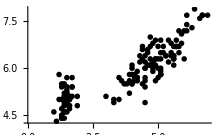
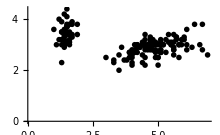
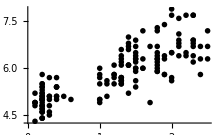
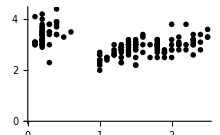
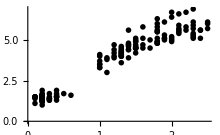
|  | 
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
Table[ListPlot[Partition[Table[{ld[[i,k]],ld[[i,p]]},{i,1,150}],50],ImageSize->220,PlotStyle->PointSize[0.02]],{k,1,4},{p,1,k-1}]//Grid
```

Из диаграмм заключаем, что наиболее информативными являются 3 и 4 признаки (нижняя правая диаграмма). При вычислении расстояния между объектами будем опираться только на них.

Разобьем всю изучающую выборку на собственно обучающую подвыборку (learn), далее обучающей выборкой будем называть именно её, и на контрольную выборку, на основании которой будем судить об успешности полученного алгоритма. Разобьем в пропорции приблизительно 2:1, так чтобы представителей разных классов было равное количество. Также заменим названия классов на их порядковые номера (“Iris-setosa”→1,”Iris-versicolor”→2,”Iris-virginica”→3)

```mathematica
learn=Flatten[Table[Partition[ld,50][[i]][[1;;33]],{i,1,3}],1]/.{"Iris-setosa"->1,"Iris-versicolor"->2,"Iris-virginica"->3};
```

```mathematica
kontrol=Flatten[Table[Partition[ld,50][[i]][[34;;50]],{i,1,3}],1]/.{"Iris-setosa"->1,"Iris-versicolor"->2,"Iris-virginica"->3};
```

```mathematica
Length[kontrol]
```

51

Запишем функцию расстояния:

```mathematica
r[u_,x_]:=Sum[(u[[i]]-x[[i]])^2,{i,3,4}]
```

Теперь составим две функции весов, одну для метода ближайшего соседа, другую для метода k-ближайших соседей:

```mathematica
w1[i_]:=Boole[i==1]
```

```mathematica
wk[i_,k_]:=Boole[i≤k]
```

Составим функцию гамма для метода ближайшего соседа:

```mathematica
gamma1[y_,u_,data_]:=Module[{sort},
sort=SortBy[data,r[u,#]&];
Boole[y==sort[[1]][[5]]]]
```

Примечание: функция SortBy является встроенной и сортирует список data на основе функции r(u,x_i) (т.е. по возрастанию расстояния от объекта u).

Теперь составим решающую функцию a(u,X^l) обозначив ее oNN (one nearest neighbor) на основе формулы (1):

```mathematica
oNN[u_,data_]:=ArgMax[{gamma1[y,u,data],y∈Integers&&1≤y≤3},y]
```

Теперь применим эту функцию к каждому элементу контрольной выборки и представим в виде таблицы:

```mathematica
Grid[Transpose@Table[{kontrol[[i]][[5]],oNN[kontrol[[i]],learn]},{i,1,Length[kontrol]}],ItemSize->.4]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3

Первая строчка - реальный класс i-ого элемента, вторая - определяемый методом ближайшего соседа.

Как мы видим, присутствуют некоторое количество ошибок. Данные точки можно даже рассмотреть на диаграмме рассеяния, это те что находятся среди множества чужих объектов.

Построим для наглядности разделяющие поверхности поверх точек контрольной выборки:

```mathematica
Show[DensityPlot[oNN[{0,0,x,z},learn],{x,1,6},{z,0,3},PlotLegends->Automatic],ListPlot[Partition[Table[{#[[i,3]],#[[i,4]]},{i,1,51}],17]]&[kontrol]]
```

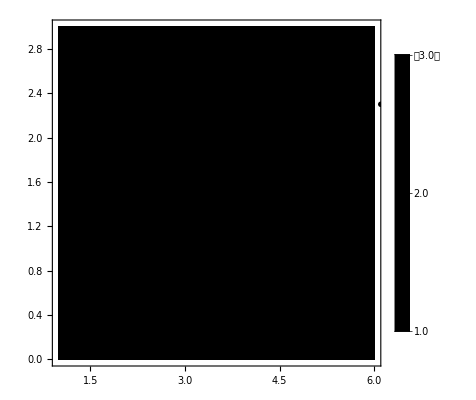

Рассмотрим также, как будет выглядеть разделяющая поверхность в случае использования метода k-ближайших соседей. Для этого составим функцию гамма:

```mathematica
gamma[y_,u_,data_,k_]:=Module[{sort},
sort=SortBy[data,r[u,#]&];
Sum[wk[i,k]Boole[y==sort[[i]][[5]]],{i,1,Length[data]}]
]
```

И запишем алгоритм:

```mathematica
kNN[u_,data_,k_]:=ArgMax[{gamma[y,u,data,k],y∈Integers&&1≤y≤3},y]
```

Составим таблицу ответов, при k=5:

```mathematica
Grid[Transpose@Table[{kontrol[[i]][[5]],kNN[kontrol[[i]],learn,5]},{i,1,Length[kontrol]}],ItemSize->.4]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3

Как мы видим, с увеличением количества соседей, точность данного метода повышается. Вновь отобразим разделяющую поверхность:

```mathematica
Show[DensityPlot[kNN[{0,0,x,z},learn,5],{x,1,6},{z,0,3},PlotLegends->Automatic],ListPlot[Partition[Table[{#[[i,3]],#[[i,4]]},{i,1,51}],17]]&[kontrol]]
```

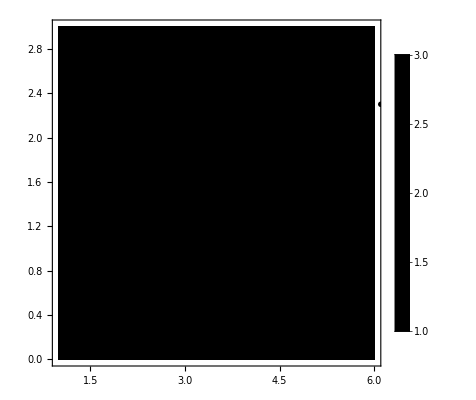

Как мы видим, форма поверхности изменилась.

В итоге имеем решающую функцию (kNN) которая на основе обучающей выборки классифицирует цветки Ириса в один из классов.